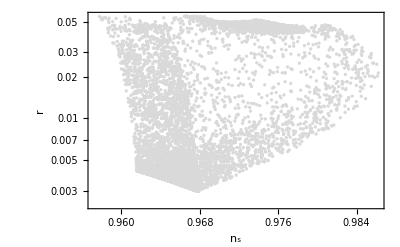

```mathematica
xi1000=Import["A:\\Sir_Mansoor_PACT_Exp\\total.txt","Table"];
df1000=ListLogPlot[Table[{xi1000[[jj,6]],xi1000[[jj,7]]},{jj,1,Length[xi1000]}],Frame->True,PlotStyle->{LightGray,PointSize[0.00601]}, PlotRange->All,FrameLabel->{Style["n_s",16,Directive[Black]],Style["r",16,Directive[Black]]}]
```

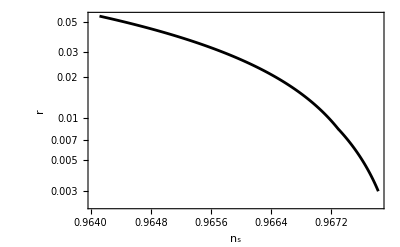

```mathematica
xi100d=Import["A:\\Sir_Mansoor_PACT_Exp\\final_Data\\kappa_0_60.dat","Table"]
d100d=Table[{xi100d[[jj,6]],xi100d[[jj,7]]},{jj,1,Length[xi100d]}];
df100d=ListLogPlot[d100d,PlotRange-> All,Joined->True,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Black,Thickness[0.005]}]
```

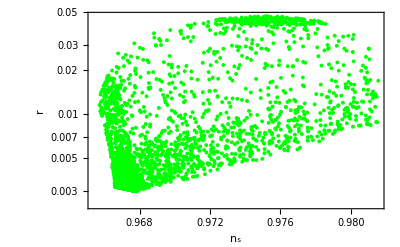

```mathematica
bound1=Import["A:\\Sir_Mansoor_PACT_Exp\\filtered_points_inside5sigma.dat","Table"];
b1=Table[{bound1[[jj,6]],bound1[[jj,7]]},{jj,1,Length[bound1]}];
p2=ListLogPlot[b1,PlotRange-> All,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Green,PointSize[0.00701]}]
```

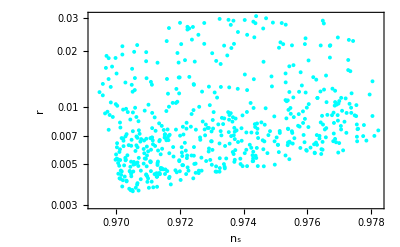

```mathematica
bound2=Import["A:\\Sir_Mansoor_PACT_Exp\\filtered_points_inside1sigma.dat","Table"];
b2=Table[{bound2[[jj,6]],bound2[[jj,7]]},{jj,7,Length[bound2]}];
p3=ListLogPlot[b2,PlotRange-> All,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{ Cyan,PointSize[0.00701]}]
```

```mathematica
4
```

4

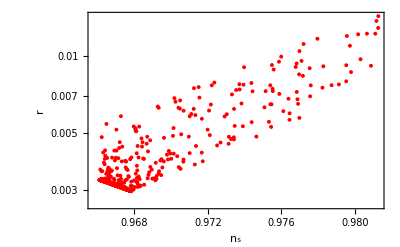

```mathematica
xi100q=Import["A:\\Sir_Mansoor_PACT_Exp\\mp_le.dat","Table"];
d100q=Table[{xi100q[[jj,6]],xi100q[[jj,7]]},{jj,7,Length[xi100q]}];
df100q=ListLogPlot[d100q,PlotRange-> All,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Red,PointSize[0.00701]}]
```

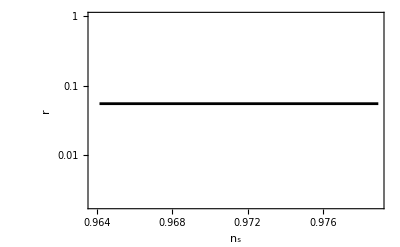

```mathematica
xi100ft=Import["A:\\Sir_Mansoor_PACT_Exp\\r_fix_kappa_60.dat","Table"];
d100ft=Table[{xi100ft[[jj,6]],xi100ft[[jj,7]]},{jj,7,Length[xi100ft]}];
df100ft=ListLogPlot[d100ft,PlotRange-> All,Joined->True,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Black,Thickness[0.005]}]
```

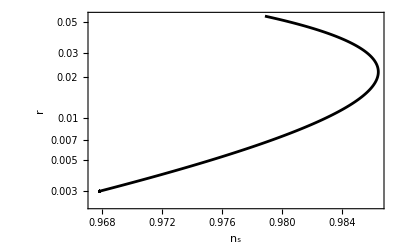

```mathematica
xi100ft1=Import["A:\\Sir_Mansoor_PACT_Exp\\final_Data\\xi_10000_60.dat","Table"]
d100ft1=Table[{xi100ft1[[jj,6]],xi100ft1[[jj,7]]},{jj,7,Length[xi100ft1]}];
df100ft1=ListLogPlot[d100ft1,PlotRange-> All,Joined->True,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Black,Thickness[0.005]}]
```

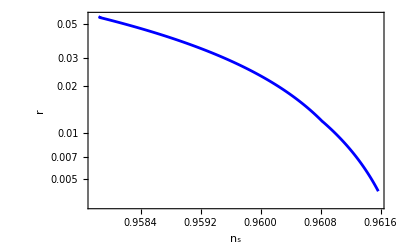

```mathematica
p50=Import["A:\\Sir_Mansoor_PACT_Exp\\final_Data\\kappa_0_50.dat","Table"];
p501=Table[{p50[[jj,6]],p50[[jj,7]]},{jj,1,Length[p50]}];
p5011=ListLogPlot[p501,PlotRange-> All,Joined->True,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Blue,Thickness[0.005]}]
```

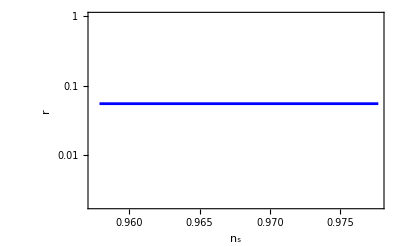

```mathematica
p50q=Import["A:\\Sir_Mansoor_PACT_Exp\\final_Data\\r_fix_kappa_50.dat","Table"];
p501q=Table[{p50q[[jj,6]],p50q[[jj,7]]},{jj,7,Length[p50q]}];
p5011q=ListLogPlot[p501q,PlotRange-> All,Joined->True,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Blue,Thickness[0.005]}]
```

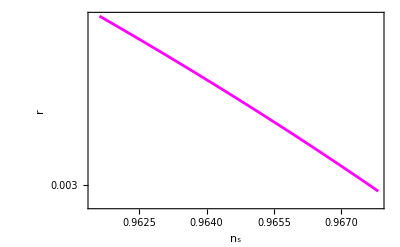

```mathematica
p50ab=Import["A:\\Sir_Mansoor_PACT_Exp\\final_Data\\xi_1000_5060.dat","Table"];
p501ab=Table[{p50ab[[jj,6]],p50ab[[jj,7]]},{jj,7,Length[p50ab]}];
p5011ab=ListLogPlot[p501ab,PlotRange-> All,Joined->True,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Magenta,Thickness[0.005]}]
```

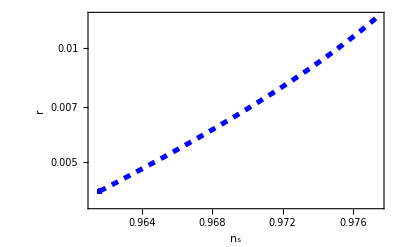

```mathematica
p50ab1=Import["A:\\Sir_Mansoor_PACT_Exp\\final_Data\\pho_corve\\xo_3_17_50.dat","Table"];
p501ab1=Table[{p50ab1[[jj,6]],p50ab1[[jj,7]]},{jj,1,Length[p50ab1]}];
p5011ab1=ListLogPlot[p501ab1,PlotRange-> All,Joined->True,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Blue, Dashed, Thickness[0.009]}]
```

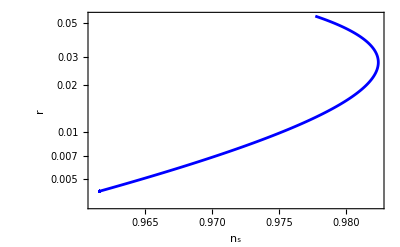

```mathematica
x1=Import["A:\\Sir_Mansoor_PACT_Exp\\final_Data\\xi_10000_50.dat","Table"];
p501ab1z=Table[{x1[[jj,6]],x1[[jj,7]]},{jj,1,Length[x1]}];
p5011ab1z=ListLogPlot[p501ab1z,PlotRange-> All,Joined->True,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Blue,Thickness[0.005]}]
```

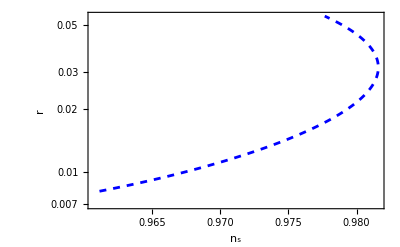

```mathematica
x11=Import["A:\\Sir_Mansoor_PACT_Exp\\final_Data\\pho_corve\\xo_39_19_50.dat","Table"];
p501ab1z1=Table[{x11[[jj,6]],x11[[jj,7]]},{jj,1,Length[x11]}];
p5011ab1z1=ListLogPlot[p501ab1z1,PlotRange-> All,Joined->True,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Blue, Dashed, Thickness[0.005]}]
```

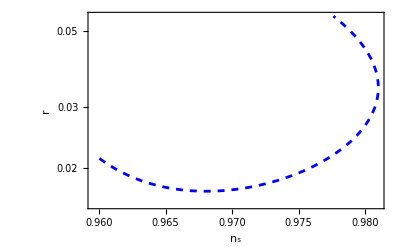

```mathematica
x11aq1=Import["A:\\Sir_Mansoor_PACT_Exp\\final_Data\\pho_corve\\xo_45_19_50.dat","Table"];
p5q1=Table[{x11aq1[[jj,6]],x11aq1[[jj,7]]},{jj,7,Length[x11aq1]}];
p5u1=ListLogPlot[p5q1,PlotRange-> All,Joined->True,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Blue, Dashed,Thickness[0.005]}]
```

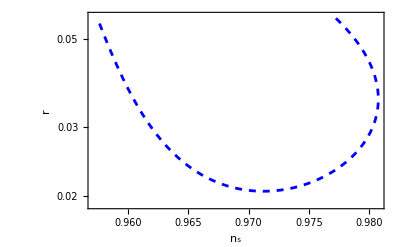

```mathematica
x11aq=Import["A:\\Sir_Mansoor_PACT_Exp\\final_Data\\pho_corve\\xo_48_19__50.dat","Table"];
p5q=Table[{x11aq[[jj,6]],x11aq[[jj,7]]},{jj,4,Length[x11aq]}];
p5u=ListLogPlot[p5q,PlotRange-> All,Joined->True,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Blue, Dashed,Thickness[0.005]}]
```

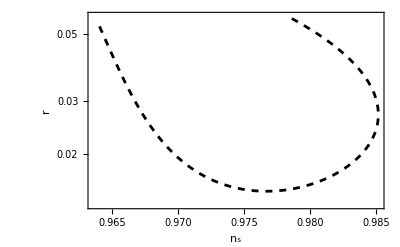

```mathematica
x11aq11=Import["A:\\Sir_Mansoor_PACT_Exp\\final_Data\\pho_corve\\xo_53_19_60.dat","Table"];
p5q11=Table[{x11aq11[[jj,6]],x11aq11[[jj,7]]},{jj,7,Length[x11aq11]}];
p5u11=ListLogPlot[p5q11,PlotRange-> All,Joined->True,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Black, Dashed, Thickness[0.005]}]
```

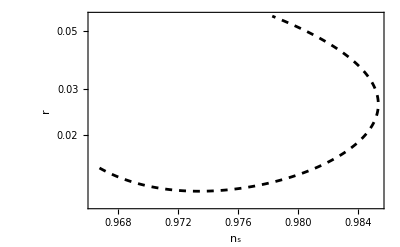

```mathematica
x11aq11a=Import["A:\\Sir_Mansoor_PACT_Exp\\final_Data\\pho_corve\\xo_49_19_60.dat","Table"];
p5q11a=Table[{x11aq11a[[jj,6]],x11aq11a[[jj,7]]},{jj,7,Length[x11aq11a]}];
p5u11a=ListLogPlot[p5q11a,PlotRange-> All,Joined->True,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Black, Dashed,Thickness[0.005]}]
```

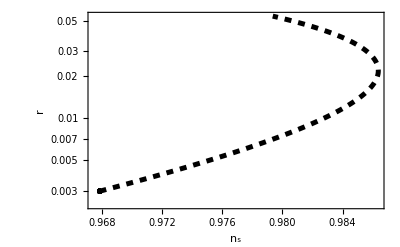

```mathematica
x11aq11ab=Import["A:\\Sir_Mansoor_PACT_Exp\\final_Data\\pho_corve\\xo_mp_60.dat","Table"];
p5q11ab=Table[{x11aq11ab[[jj,6]],x11aq11ab[[jj,7]]},{jj,7,Length[x11aq11ab]}];
p5u11ab=ListLogPlot[p5q11ab,PlotRange-> All,Joined->True,Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Black, Dashed, Thickness[0.009]}]
```

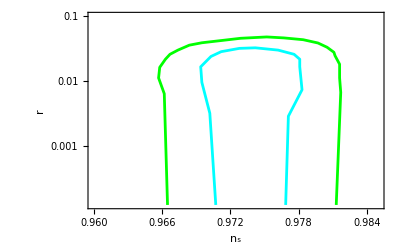

```mathematica
(*massco1=Select[neu,(MASS[1000024]≥103.5&&MASS[1000037]≥103.5&&MASS[1000015]≥105&&MASS[1000005]≥100&&
MASS[1000006]≥100&&MASS[2000001]≥2000&&MASS[1000001]≥2000&&MASS[1000002]≥2000&&MASS[2000002]≥2000&&MASS[1000021]≥2300)/.#&];
Length[massco1]*)
(*Import the data*)data1=Import["A:\\Sir_Mansoor_PACT_Exp\\PA1.txt","Table"];
data5=Import["A:\\Sir_Mansoor_PACT_Exp\\PA5.txt","Table"];
Q90=Table[{data1[[jj,1]],data1[[jj,2]]},{jj,1,Length[data1]}];
Q91=Table[{data5[[jj,1]],data5[[jj,2]]},{jj,1,Length[data5]}];
P6=ListLogPlot[{Q90,Q91},Joined->True,PlotRange-> {{0.96,0.985},{0.00,0.1}},Frame->True,FrameLabel->{Subscript[n, s],r},PlotStyle->{Cyan,Green}]
```

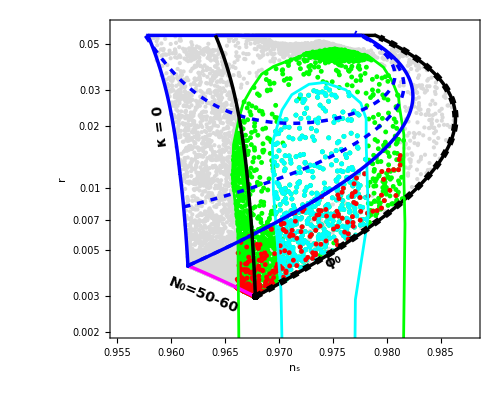

```mathematica
Show[df1000,p2,p3,df100q,df100ft,df100ft1,p5011,p5011q,p5011ab,p5011ab1,P6,p5011ab1z,p5011ab1z1,p5u,df100d,p5u11ab,Graphics[{Text[Style[Rotate["κ = 0",1.081π/2],Bold,14],{0.959,Log[0.02]}  (*Adjust this coordinate as needed*)],Text[Style[Rotate["ϕ_0",π/7],Bold,14],{0.975,Log[0.0044]}  (*Adjust this coordinate as needed*)],Text[Style[Rotate["N_0=50-60",1.25*3π/2],Bold,14],{0.963,Log[0.003]}  (*Adjust this coordinate as needed*)]}],PlotRange-> {{0.955,0.988},{Log[0.002],Log[0.061]}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],LabelStyle->{FontWeight->"Bold",FontSize->14},TicksStyle->Directive[Bold],AspectRatio->0.8,FrameLabel->{Style["\!\(\*SubscriptBox[\(n\), \(s\)]\)",16,Directive[Black]],Style["r",16,Directive[Black]]},Axes->False,ImageSize->500]
```

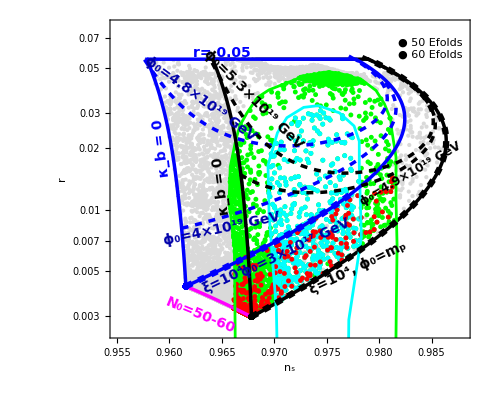

```mathematica
Show[df1000,p2,p3,df100q,df100ft,df100ft1,p5011,p5011q,p5011ab,p5011ab1,P6,p5011ab1z,p5011ab1z1,p5u,df100d,p5u11,p5u11a,p5u11ab,Graphics[{(*Existing Text Annotations*)Text[Style[Rotate["κ_b = 0",1.081 π/2],Bold,14, Blue],{0.9592,Log[0.02]}],Text[Style[Rotate["κ_b = 0",1.081 π/2],Bold,14],{0.965,Log[0.013]}],
Text[Style[Rotate["r= 0.05",0],Bold,14,Blue],{0.965,Log[0.059]}],
Text[Style[Rotate["ξ=10^4",π/7],Bold,14, Darker[Blue]],{0.9652,Log[0.0045]}],Text[Style[Rotate["ϕ_0=3×10^17 GeV",π/7],Bold,14, Darker[Blue]],{0.972,Log[0.0065]}],
Text[Style[Rotate["ϕ_0=4×10^19 GeV",π/15],Bold,14, Darker[Blue]],{0.965,Log[0.008]}],
Text[Style[Rotate["ϕ_0=4.8×10^19 GeV",-π/5],Bold,14, Darker[Blue]],{0.963,Log[0.035]}],


Text[Style[Rotate["ξ=10^4, ϕ_0=m_p",π/7],Bold,14],{0.978,Log[0.0052]}],
Text[Style[Rotate["ϕ_0=5.3×10^19 GeV",-π/4],Bold,14],{0.968,Log[0.035]}],
Text[Style[Rotate["ϕ_0=4.9×10^19 GeV",π/6],Bold,12],{0.983,Log[0.015]}],





Text[Style[Rotate["\!\(\*SubscriptBox[\(N\), \(0\)]\)=50-60",1.25*3 π/2],Bold,14,Magenta],{0.963,Log[0.003]}],(*Custom Legend Box*)Inset[Framed[Column[{Row[{Style["●",Blue,Bold,14],Style[" 50 Efolds",Bold,14]}],Row[{Style["●",Black,Bold,14],Style[" 60 Efolds",Bold,14]}]},Alignment->Left,Spacings->0.5],Background->White,RoundingRadius->5,FrameStyle->Gray],Scaled[{0.89,0.91}]  (*adjust position*)]}],PlotRange->{{0.955,0.988},{Log[0.0025],Log[0.08]}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],LabelStyle->{FontWeight->"Bold",FontSize->17},TicksStyle->Directive[Bold],AspectRatio->0.8,FrameLabel->{Style["\!\(\*SubscriptBox[\(n\), \(s\)]\)",19,Directive[Black]],Style["r",19,Directive[Black]]},Axes->False,ImageSize->500]
```

```mathematica
2
```

2